```mathematica
As:={{0,1},{0,0}}
Cs:={{1,0}}
xs:={{p[t]},{D[p[t],t]}}
eq:=D[xs,t]==As.xs
y:=Cs.xs
MatrixForm[As]
MatrixForm[Cs]
MatrixForm[eq]
MatrixForm[y]
```

(0 | 1
0 | 0)

(1 | 0)

{{p'[t]},{p''[t]}}=={{p'[t]},{0}}

(p[t])

```mathematica
K:={{k1},{k2}}
MatrixForm[K]
xHat:={{pHat[t]},{pHatd[t]}}
eqHat:=Thread[D[xHat,t]==A . xHat+K . (y-Cs . xHat)]
MatrixForm[eqHat]
```

(k1
k2)

({pHat'[t]}=={k1 (p[t]-pHat[t])+pHatd[t]}
{pHatd'[t]}=={k2 (p[t]-pHat[t])})

```mathematica
pHatLaplace=Thread[LaplaceTransform[eqHat[[1]],t,s]][[1]]/.{pHat[0]->0,pHat'[0]->0}
```

s LaplaceTransform[pHat[t],t,s]==k1 LaplaceTransform[p[t],t,s]-k1 LaplaceTransform[pHat[t],t,s]+LaplaceTransform[pHatd[t],t,s]

```mathematica
pHatSol=Solve[pHatLaplace,LaplaceTransform[pHat[t],t,s]]
```

{{LaplaceTransform[pHat[t],t,s]→(k1 LaplaceTransform[p[t],t,s]+LaplaceTransform[pHatd[t],t,s])/(k1+s)}}

```mathematica
pHatdLaplace=Thread[LaplaceTransform[eqHat[[2]],t,s]][[1]]/.{pHatd[0]->0}/.pHatSol
```

{s LaplaceTransform[pHatd[t],t,s]==k2 (LaplaceTransform[p[t],t,s]-(k1 LaplaceTransform[p[t],t,s]+LaplaceTransform[pHatd[t],t,s])/(k1+s))}

```mathematica
pHatdSol=Solve[pHatdLaplace,LaplaceTransform[pHatd[t],t,s]]
```

{{LaplaceTransform[pHatd[t],t,s]→(k2 s LaplaceTransform[p[t],t,s])/(k2+k1 s+s^2)}}

```mathematica
pHatdSol[[1]][[1]][[2]]
```

(k2 s LaplaceTransform[p[t],t,s])/(k2+k1 s+s^2)

```mathematica
pHatdTF=TransferFunctionModel[{{pHatdSol[[1]][[1]][[2]]/LaplaceTransform[p[t],t,s]}},s]
```

((k2 s)/(k2+k1 s+s^2))_^𝒯

```mathematica
bodePlotOptions={GridLines->Automatic,PlotLabel->{"Magnitude Plot","Phase Plot"}}
```

{GridLines→Automatic,PlotLabel→{Magnitude Plot,Phase Plot}}

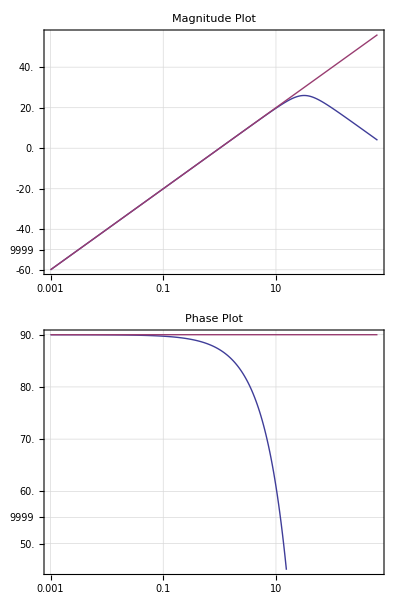

```mathematica
BodePlot[{pHatdTF/.{k1->50,k2->1000},TransferFunctionModel[{{s}},s]},bodePlotOptions]
```

```mathematica
TransferFunctionPoles[pHatdTF][[1]][[1]]
```

{1/2 (-k1-√(k1^2-4 k2)),1/2 (-k1+√(k1^2-4 k2))}

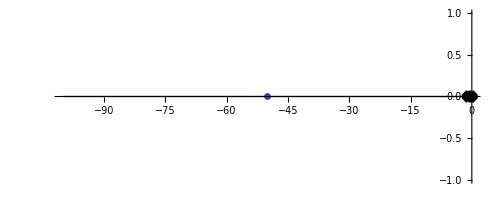

```mathematica
RootLocusPlot[pHatdTF/.{k1->1},{k2,0,100}]
```